# Report Project X

Course code: IX12500
Date: 2018-09-14

Michel Ouadria, ouadria@kth.se
Rikard Jakobsson, rikjak@kth.se

Task 1: Probability Experiment

## Summary

### Task

Assume that you play a variant of a poker game with five cards that is using a subset of two ordinary deck of cards. The subset considered is cards valued 9,10,J,Q,K,A from the two decks, in total 48 cards.

Calculate the exact probability of the following hands using the  census method.

If a given hand contains different valued hands only one (the highest rank) is considered.

One pair

Two pairs

Three of a kind

Four of a kind

Five of a kind

Full hand

Straight

Flush

Straight flush

Nothing

### Result

●Straight Flush:
	• 256
	• 0.0149506%

●Straight:
	• 65 280
	• 3.81241%

●Full House:
	• 47 040
	• 2.74718%
	
●Five of a kind:
	• 336
	• 0.0196227%
	
●Four of a kind:
	• 16 800
	• 0.981134%
	
●Flush:
	• 2912
	• 0.170063%
	
●Three of a kind:
	• 215 040
	• 12.5585%
	
●Two pairs:
	• 37 5840
	• 21.9494%
	
●One pair:
	• 85 8240
	• 50.1219%
	
●Nothing:
	• 130 560
	• 50.1219%

### Discussion

## Road Construction?????????

### Model for cross section area

The data is interpolated as a function A(x).

### Model for volume

The requested volume to be transported can be calculated numerically with the integral

I.e. about 0.1 km^3 must be transported.

### Code

```mathematica
Quit[];
```

```mathematica
deck = {109,109,110,110,111,111,112,112,113,113,114,114,209,209,210,210,211,211,212,212,213,213,214,214,309, 309,310,310,311,
311,312,312,313,313,314,314,409,409,410,410,411,411,412,412,
413,413,414,414};

hand = Subsets[deck,{5}](*Sort deck with all subsets containing 5*)
sizeOfPermutations = Length[hand] (*Amount of different possible hands*)
```

{{109,109,110,110,111},{109,109,110,110,111},{109,109,110,110,112},{109,109,110,110,112},{109,109,110,110,113},{109,109,110,110,113},{109,109,110,110,114},{109,109,110,110,114},{109,109,110,110,209},1712287,{411,412,413,414,414},{411,413,413,414,414},{412,412,413,413,414},{412,412,413,413,414},{412,412,413,414,414},{412,412,413,414,414},{412,413,413,414,414},{412,413,413,414,414}}
 |  |  |  |

1712304

#### Straight flush

```mathematica
straightFlushQ[h_]:=MatchQ[h-h[[1]],{0,1,2,3,4}]
straightFlush =Count[hand, _?(straightFlushQ)]
N[straightFlush/sizeOfPermutations]*100
```

256

0.0149506

#### Straight

```mathematica
straightQ[{9,10,11,12,13}]:=True;(*All possible hands from 9 to K = True*)
straightQ[{10,11,12,13,14}]:=True;(*All possible hands from 10 to A = True *)
straightQ[{___}]:=False(*All other possibilities = False*)
straightRemoveSuiteQ[hand_]:= straightQ[Sort[Mod[hand,100]]]; (*Calculating suites by removing the first digit from all cards in the deck, i.e 109 = 9 ...*)
straight =(Count[hand,_?(straightRemoveSuiteQ)]-straightFlush) (*Final result of all the chances of getting straight. Subtract Straight flush since the cases above doesn't exclude it as a possibility*)
N[(straight)/sizeOfPermutations]*100 (*Probability*)
```

65280

3.81241

#### Full house

```mathematica
fullHouseQ[{x_,x_,x_,y_,y_}/;x≠y]:=True;(*Check for three of a kind and a pair, they can't be the same rank!!!!!!!!!*)
fullHouseQ[{x_,x_,y_,y_,y_}/;x≠y]:=True;(*Second scenario*)
fullHouseQ[___]:=False;(*Everything else is excluded*)
fullHouseRemoveSuiteQ[hand_]:=fullHouseQ[Sort[Mod[hand,100]]]
fullHouse =Count[hand,_?(fullHouseRemoveSuiteQ)]
N[fullHouse/sizeOfPermutations]*100
```

47040

2.74718

#### Five of a kind

```mathematica
fiveOfAKindQ[{x_,x_,x_,x_,x_}]:=True;(*Check for five of a kind*)
fiveOfAKindQ[{___}]:=False;(*Exclude everything else*)
fiveOfAKindRemoveSuiteQ[hand_]:=fiveOfAKindQ[Sort[Mod[hand,100]]]
fioak = Count[hand,_?(fiveOfAKindRemoveSuiteQ)]
N[fioak/sizeOfPermutations]*100
```

336

0.0196227

#### Four of a kind

```mathematica
fourOfAKindQ[{x_,x_,x_,x_,y_}/;x≠y]:=True; 
fourOfAKindQ[{y_,x_,x_,x_,x_}/;x≠y]:=True; 
fourOfAKindQ[{___}]:=False;
fourOfAKindRemoveSuiteQ[hand_]:=fourOfAKindQ[Sort[Mod[hand,100]]];
foak = Count[hand,_?(fourOfAKindRemoveSuiteQ)]
N[foak/sizeOfPermutations]*100
```

16800

0.981134

#### Flush

```mathematica
flushQ[h_]:=MatchQ[(h-h[[1] ]),{0,0,0,0,0}](**)
flushGetSuiteQ[hand_]:= flushQ[Quotient[hand,100]](*Get the suite through quotienet function. I.e 109 = 100!!!!!!!*)
flush=Count[hand,_?(flushGetSuiteQ)]- straightFlush
N[flush/sizeOfPermutations]*100
```

2912

0.170063

#### Three of a kind

```mathematica
threeOfAKindQ[{___,x_,x_,x_,x_,___}]:=False; (*Four of a kind excluded*)
threeOfAKindQ[{x_,x_,y_,y_,y_}/;x≠y]:=False;(*Full house excluded*)
threeOfAKindQ[{x_,x_,x_,y_,y_}/;x≠y]:=False;(*Second scenario of full house*)
threeOfAKindQ[{___,x_,x_,x_,___}]:=True; (*Three of a kind*)
threeOfAKindQ[{___}]:=False; 
threeOfAKindRemoveSuiteQ[hand_]:=threeOfAKindQ[Sort[Mod[hand,100]]];
threePair =Count[hand,_?(threeOfAKindRemoveSuiteQ)]
N[threePair/sizeOfPermutations]*100
```

215040

12.5585

#### Two Pair Flush

```mathematica
twoPairQ[{x_,x_,y_,y_,z_}/;x≠y≠z]:=True;(*Two pair*)
twoPairQ[{z_,x_,x_,y_,y_}/;x≠y≠z]:=True;(*Second scenario*)
twoPairQ[{x_,x_,z_,y_,y_}/;x≠y≠z]:=True;(*Third senario*)
twoPairQ[{___}]:=False;
twoPairRemoveSuiteQ[hand_]:=twoPairQ[Sort[Mod[hand,100]]];
(*Check when a hand with two pair without suite are the same as the flush suite*)
twoPairWithFlushQ[hand_]:=twoPairRemoveSuiteQ[hand]&&flushGetSuiteQ[hand]
twoPairwithFlush = Count[hand,_?(twoPairWithFlushQ)]
```

480

#### Two pair

```mathematica
(*Go through all possible cases of twoPair excl. suite and excl. cases where two pair are of same suite*)
twoPair = Count[hand,_?(twoPairRemoveSuiteQ)]-twoPairwithFlush

N[twoPair/sizeOfPermutations]*100
```

375840

21.9494

#### One pair

```mathematica
pairQ[{x_,x_,y_,z_,w_}/;x≠y≠z≠w]:=True;(* First case of two pairs *)
pairQ[{y_,x_,x_,z_,w_}/;x≠y≠z≠w]:=True;(*Second case*)
pairQ[{y_,z_,x_,x_,w_}/;x≠y≠z≠w]:=True;(*Third case*)
pairQ[{y_,z_,w_,x_,x_}/;x≠y≠z≠w]:=True;(*Fourth case*)
pairQ[{___}]:=False (* else *)

pairRemoveSuiteQ[hand_]:=pairQ[Sort[Mod[hand,100]]]
pairWithFlushQ[hand_]:=pairRemoveSuiteQ[hand]&&flushGetSuiteQ[hand]
pairWithFlush = Count[hand,_?(pairWithFlushQ)];
onePair = Count[hand,_?(pairRemoveSuiteQ)]-pairWithFlush
N[onePair/sizeOfPermutations]*100
```

858240

50.1219

#### Nothing

```mathematica
noHand = Length[hand] -straightFlush - straight-flush-fullHouse-foak-threePair-fioak-twoPair-onePair
N[noHand/sizeOfPermutations]*100
```

130560

7.62481

Task 2: Combinatorial Calculus & Monte Carlo Experiment

## Summary

### Task

Consider the following C of the probability of getting four of a kind. In this case we are dealing with sampling without replacement and without regard to order. First choose one of six possibilities {9,…,A} to be the kind value x, then we choose four out of the eight x and finally we add a last card from the remaining 40. The multiplication principle gives the result.

### Result

Straight Flush:  2^5 Binomial[2, 1] Binomial[4, 1] = 256
Probability: 0.0149506%

Straight: Binomial[2, 1] Binomial[8, 1]^5- Straight Flush = 65 280
Probability: 3.81241%

Full House: Binomial[6, 1] Binomial[8, 3]Binomial[5, 1]Binomial[8, 2] = 47 040
Probability: 2.74718%

Flush: Binomial[12, 5] Binomial[4, 1] - Straight Flush = 2912
Probability: 0.170063%

Four of a kind: Binomial[6, 1] Binomial[8, 4]Binomial[40, 1] = 16 800
Probability: 0.981134%

Three of a kind: Binomial[6, 1] Binomial[8, 3]Binomial[5, 2]Binomial[8, 1]^2 = 215 040
Probability: 12.5585%

The result from the combinatorial calculations verifies the same probability as the census method.

## Code

### Deck

```mathematica
deckC=Binomial[48, 5]
```

1712304

### Straight Flush

The straight flush can start with possible cards, nine or ten, and can be of four possible suites.

```mathematica
straightFlushC=2^5 Binomial[2, 1] Binomial[4, 1]
```

256

```mathematica
N[(2^5 Binomial[2, 1] Binomial[4, 1])/deckC]*100
```

0.0149506

### Straight

The straight applies same principle above with the exception of flush, no sequence of five suites. 
Binomial[2, 1] = Two possible starting cards, pick one. Binomial[8, 1]=Eight possible suites, including recurrence of same suite, pick one. Repeat five times. Exclude the possibility of flush and straight appearing together.

```mathematica
straightC=Binomial[2, 1] Binomial[8, 1]^5;
straightC - straightFlushC
```

```mathematica
N[(Binomial[2, 1] Binomial[8, 1]^5-2^5 Binomial[2, 1] Binomial[4, 1])/deckC]*100
```

3.81241

### Full House

The full house consists of three of kind and a pair of two in the same hand.
Binomial[6, 1]=Pick one out of six possible ranks.Binomial[8, 3]=Pick three out of eight possible suites, including recurrence of same suite.Binomial[5, 1]=Pick one out of the remaining five cards.Binomial[8, 2]=Pick two out of eight possible suites, including recurrence of same suite.

```mathematica
fullHouseC=Binomial[6, 1] Binomial[8, 3]Binomial[5, 1]Binomial[8, 2]
```

47040

```mathematica
N[(Binomial[6, 1] Binomial[8, 3]Binomial[5, 1]Binomial[8, 2])/deckC]*100
```

2.74718

### Flush

The flush consists of a hand with hand of where all cards holds same suite, but not pair or straight of the rank.
Binomial[12, 5]=Pick five out of the 12 possible suites!!!!!!!!!Binomial[4, 1]=Pick one

```mathematica
flushC=Binomial[12, 5] Binomial[4, 1] ;
flushC-straightFlushC
```

```mathematica
N[(Binomial[12, 5] Binomial[4, 1]- 2^5 Binomial[2, 1] Binomial[4, 1])/deckC]*100
```

0.170063

### Four of a kind

```mathematica
fourOfAKindC=Binomial[6, 1] Binomial[8, 4]Binomial[40, 1]
```

```mathematica
N[(Binomial[6, 1] Binomial[8, 4]Binomial[40, 1])/deckC]*100
```

0.981134

### Three of a kind

```mathematica
threeOfAKindC=Binomial[6, 1] Binomial[8, 3]Binomial[5, 2] Binomial[8, 1]^2
```

```mathematica
N[(Binomial[6, 1] Binomial[8, 3]Binomial[5, 2] Binomial[8, 1]^2)/deckC]*100
```

12.5585

## Summary

### Task

Estimate the probability of one pair using the Monte Carlo method. Draw a diagram that shows how the probability estimate stabilises with increasing sample size.

### Result

jkhhkkh j hkjhk(* *)

## Code

```mathematica
monteCarlo[h_]:=(counter = 0;
For[i=1,i≤h,i++,
chosenHand = RandomChoice[hand];
If[(pairRemoveSuiteQ[chosenHand]&&Not[pairWithFlushQ[chosenHand]]),counter++]
];
N[counter/h])

array=Range[10000];
(*Run monte carlo 1000 times*)
For[j=1, j<=10000,j++,
array[[j]] = monteCarlo[j^1.5];
];
array(*Print array*)
```

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100,101,102,103,104,105,106,107,108,109,110,111,112,113,114,115,116,117,118,119,120,121,122,123,124,125,126,127,128,129,130,131,132,133,134,135,136,137,138,139,140,141,142,143,144,145,146,147,148,149,150,151,152,153,154,155,156,157,158,159,160,161,162,163,164,165,166,167,168,169,170,171,172,173,174,175,176,177,178,179,180,181,182,183,184,185,186,187,188,189,190,191,192,193,194,195,196,197,198,199,200,201,202,203,204,205,206,207,208,209,210,211,212,213,214,215,216,217,218,219,220,221,222,223,224,225,226,227,228,229,230,231,232,233,234,235,236,237,238,239,240,241,242,243,244,245,246,247,248,249,250,251,252,253,254,255,256,257,258,259,260,261,262,263,264,265,266,267,268,269,270,271,272,273,274,275,276,277,278,279,280,281,282,283,284,285,286,287,288,289,290,291,292,293,294,295,296,297,298,299,300,301,302,303,304,305,306,307,308,309,310,311,312,313,314,315,316,317,318,319,320,321,322,323,324,325,326,327,328,329,330,331,332,333,334,335,336,337,338,339,340,341,342,343,344,345,346,347,348,349,350,351,352,353,354,355,356,357,358,359,360,361,362,363,364,365,366,367,368,369,370,371,372,373,374,375,376,377,378,379,380,381,382,383,384,385,386,387,388,389,390,391,392,393,394,395,396,397,398,399,400,401,402,403,404,405,406,407,408,409,410,411,412,413,414,415,416,417,418,419,420,421,422,423,424,425,426,427,428,429,430,431,432,433,434,435,436,437,438,439,440,441,442,443,444,445,446,447,448,449,450,451,452,453,454,455,456,457,458,459,460,461,462,463,464,465,466,467,468,469,470,471,472,473,474,475,476,477,478,479,480,481,482,483,484,485,486,487,488,489,490,491,492,493,494,495,496,497,498,499,500,501,502,503,504,505,506,507,508,509,510,511,512,513,514,515,516,517,518,519,520,521,522,523,524,525,526,527,528,529,530,531,532,533,534,535,536,537,538,539,540,541,542,543,544,545,546,547,548,549,550,551,552,553,554,555,556,557,558,559,560,561,562,563,564,565,566,567,568,569,570,571,572,573,574,575,576,577,578,579,580,581,582,583,584,585,586,587,588,589,590,591,592,593,594,595,596,597,598,599,600,601,602,603,604,605,606,607,608,609,610,611,612,613,614,615,616,617,618,619,620,621,622,623,624,625,626,627,628,629,630,631,632,633,634,635,636,637,638,639,640,641,642,643,644,645,646,647,648,649,650,651,652,653,654,655,656,657,658,659,660,661,662,663,664,665,666,667,668,669,670,671,672,673,674,675,676,677,678,679,680,681,682,683,684,685,686,687,688,689,690,691,692,693,694,695,696,697,698,699,700,701,702,703,704,705,706,707,708,709,710,711,712,713,714,715,716,717,718,719,720,721,722,723,724,725,726,727,728,729,730,731,732,733,734,735,736,737,738,739,740,741,742,743,744,745,746,747,748,749,750,751,752,753,754,755,756,757,758,759,760,761,762,763,764,765,766,767,768,769,770,771,772,773,774,775,776,777,778,779,780,781,782,783,784,785,786,787,788,789,790,791,792,793,794,795,796,797,798,799,800,801,802,803,804,805,806,807,808,809,810,811,812,813,814,815,816,817,818,819,820,821,822,823,824,825,826,827,828,829,830,831,832,833,834,835,836,837,838,839,840,841,842,843,844,845,846,847,848,849,850,851,852,853,854,855,856,857,858,859,860,861,862,863,864,865,866,867,868,869,870,871,872,873,874,875,876,877,878,879,880,881,882,883,884,885,886,887,888,889,890,891,892,893,894,895,896,897,898,899,900,901,902,903,904,905,906,907,908,909,910,911,912,913,914,915,916,917,918,919,920,921,922,923,924,925,926,927,928,929,930,931,932,933,934,935,936,937,938,939,940,941,942,943,944,945,946,947,948,949,950,951,952,953,954,955,956,957,958,959,960,961,962,963,964,965,966,967,968,969,970,971,972,973,974,975,976,977,978,979,980,981,982,983,984,985,986,987,988,989,990,991,992,993,994,995,996,997,998,999,1000}

{1.,0.707107,0.3849,0.75,0.447214,0.748455,0.539949,0.353553,0.703704,0.600833,0.465972,0.3849,0.5547,0.477252,0.361478,0.484375,0.470804,0.563067,0.495055,0.536656,0.540349,0.552384,0.489556,0.501805,0.472,0.497833,0.5132,0.5332,0.416214,0.505122,0.556197,0.541379,0.532783,0.443879,0.584364,0.50463,0.51097,0.525085,0.529655,0.537587,0.495185,0.510671,0.43267,0.496808,0.526718,0.464763,0.487251,0.514203,0.530612,0.551543,0.494217,0.533366,0.518342,0.539291,0.529553,0.505887,0.506576,0.498059,0.494277,0.509943,0.495356,0.505952,0.483955,0.46875,0.50568,0.509151,0.46315,0.483288,0.544353,0.507118,0.496442,0.509051,0.482594,0.477558,0.491133,0.48449,0.457322,0.512428,0.498457,0.496128,0.529492,0.549464,0.513115,0.513072,0.477247,0.49904,0.508945,0.524522,0.509752,0.507136,0.491888,0.497488,0.498406,0.526683,0.48923,0.491174,0.50558,0.493738,0.470033,0.495,0.497519,0.509635,0.493621,0.475204,0.500962,0.505802,0.493307,0.514091,0.493852,0.512269,0.515624,0.518857,0.512818,0.494583,0.503553,0.473843,0.490696,0.502415,0.503029,0.496754,0.533434,0.501657,0.502882,0.491018,0.504457,0.4921,0.526824,0.499947,0.49551,0.502622,0.498211,0.524871,0.508531,0.508651,0.511935,0.493058,0.507002,0.511371,0.510134,0.504678,0.492151,0.501145,0.497067,0.493056,0.498273,0.489761,0.499921,0.50375,0.529477,0.496974,0.50498,0.489866,0.499866,0.504948,0.494887,0.498861,0.502236,0.506538,0.495782,0.480765,0.49881,0.485954,0.512723,0.490424,0.493521,0.502628,0.521288,0.487709,0.500683,0.499881,0.478956,0.498724,0.483419,0.502349,0.499777,0.494667,0.499823,0.501934,0.516941,0.494005,0.503058,0.492809,0.526342,0.510838,0.507099,0.495525,0.502896,0.501605,0.511484,0.500579,0.517488,0.494281,0.504244,0.508122,0.499811,0.510569,0.504878,0.494956,0.504766,0.50947,0.501111,0.492518,0.498219,0.492157,0.516838,0.495154,0.498621,0.512031,0.496446,0.513277,0.508328,0.503439,0.517913,0.509495,0.504676,0.48889,0.505848,0.51045,0.507266,0.493698,0.493395,0.516367,0.496982,0.491868,0.49363,0.500953,0.489752,0.502799,0.507878,0.503709,0.502436,0.496927,0.503291,0.504259,0.494104,0.498138,0.512804,0.48125,0.498802,0.511288,0.499288,0.504697,0.5132,0.494831,0.505886,0.512135,0.508255,0.501599,0.502907,0.505711,0.498417,0.496203,0.489785,0.496036,0.502698,0.493652,0.508007,0.497334,0.493737,0.507111,0.503488,0.513813,0.491191,0.489102,0.506504,0.505725,0.503345,0.486626,0.509301,0.494077,0.505018,0.514942,0.501474,0.501157,0.495136,0.492884,0.498026,0.50354,0.502337,0.500929,0.501442,0.505323,0.507478,0.497905,0.508797,0.498274,0.493204,0.510484,0.502748,0.511489,0.503617,0.49502,0.495877,0.505252,0.488277,0.503085,0.50758,0.502111,0.494372,0.498253,0.508794,0.502839,0.513434,0.518072,0.499569,0.498056,0.506593,0.514858,0.507205,0.48863,0.504873,0.491561,0.498417,0.48795,0.499222,0.505043,0.496809,0.49482,0.50092,0.488616,0.498158,0.505358,0.510937,0.505316,0.499913,0.494896,0.494488,0.503675,0.509089,0.496101,0.512121,0.489476,0.508501,0.500322,0.506075,0.496673,0.500606,0.491467,0.510762,0.499578,0.503099,0.501843,0.505947,0.501234,0.512165,0.49068,0.494439,0.496468,0.500164,0.509782,0.495743,0.501052,0.503146,0.504769,0.494116,0.501266,0.493528,0.51021,0.507492,0.494399,0.48943,0.502358,0.498693,0.498799,0.504638,0.507713,0.504786,0.501738,0.497583,0.505122,0.497344,0.502587,0.496819,0.499252,0.490922,0.500212,0.502458,0.493662,0.507702,0.492875,0.509088,0.507091,0.501103,0.490111,0.509912,0.498306,0.500973,0.501916,0.49164,0.49793,0.485674,0.495928,0.496732,0.507373,0.499843,0.492494,0.50315,0.498736,0.497113,0.504125,0.499625,0.502973,0.498259,0.492839,0.499849,0.507293,0.501649,0.510241,0.499425,0.503622,0.496984,0.50534,0.504221,0.512129,0.502473,0.500308,0.50626,0.499881,0.49716,0.509559,0.498599,0.505826,0.493803,0.498128,0.505387,0.506452,0.493907,0.500309,0.509027,0.500635,0.501576,0.495938,0.496884,0.495721,0.503822,0.502419,0.498944,0.498328,0.502388,0.499376,0.499622,0.499111,0.498173,0.498094,0.509412,0.50356,0.496263,0.497344,0.498206,0.500317,0.506798,0.501163,0.505727,0.496304,0.506518,0.499204,0.50074,0.504304,0.503775,0.497471,0.506158,0.496258,0.500975,0.50626,0.504528,0.506782,0.49921,0.497907,0.49661,0.49748,0.495701,0.500465,0.499851,0.504762,0.493703,0.498118,0.495016,0.493751,0.492969,0.50265,0.499377,0.503588,0.504097,0.492487,0.503416,0.502704,0.504134,0.496926,0.503356,0.498404,0.49725,0.493261,0.490117,0.498283,0.503584,0.504054,0.512461,0.5003,0.493953,0.493098,0.503037,0.495933,0.507308,0.49811,0.500773,0.497444,0.497637,0.498352,0.493923,0.505929,0.500895,0.500119,0.505801,0.500636,0.498579,0.503529,0.494838,0.503076,0.506697,0.500092,0.503866,0.493531,0.505995,0.506131,0.501527,0.496865,0.499171,0.504182,0.508342,0.489939,0.498608,0.496306,0.504093,0.505109,0.500542,0.492615,0.493489,0.503173,0.502412,0.495837,0.503443,0.496741,0.506276,0.498812,0.50192,0.50689,0.498857,0.495309,0.499554,0.502378,0.495986,0.499265,0.50637,0.498404,0.49897,0.496862,0.504805,0.496545,0.502477,0.50098,0.496556,0.506265,0.498928,0.506262,0.498366,0.500759,0.499138,0.501219,0.509697,0.50211,0.500132,0.497652,0.502911,0.500798,0.506237,0.504485,0.503102,0.50633,0.498272,0.497271,0.499201,0.496846,0.498552,0.509743,0.501016,0.496138,0.504785,0.506304,0.505225,0.503941,0.496189,0.50493,0.49652,0.505697,0.501047,0.495457,0.500451,0.500427,0.49706,0.506092,0.501368,0.495244,0.501037,0.505249,0.500301,0.499935,0.501174,0.499605,0.507224,0.496884,0.498975,0.501584,0.50062,0.50045,0.508737,0.501285,0.501306,0.497877,0.501021,0.503502,0.501705,0.503847,0.499419,0.505661,0.505344,0.500941,0.495985,0.498296,0.495333,0.49681,0.49891,0.498986,0.504397,0.506461,0.505453,0.494099,0.499218,0.506236,0.496442,0.49775,0.500283,0.501881,0.503593,0.500462,0.50345,0.501185,0.498019,0.50305,0.499589,0.496807,0.503911,0.499389,0.497523,0.501943,0.500376,0.49828,0.502843,0.50626,0.498724,0.496824,0.500169,0.508547,0.507046,0.496783,0.501902,0.5031,0.499705,0.501074,0.499546,0.503214,0.504621,0.505332,0.506726,0.496455,0.50037,0.505007,0.502583,0.499659,0.503359,0.495933,0.50075,0.498919,0.500344,0.493098,0.498378,0.502631,0.504755,0.497006,0.504826,0.498764,0.50126,0.500229,0.504573,0.499052,0.508127,0.498428,0.504801,0.497046,0.504854,0.496915,0.496337,0.499901,0.503717,0.501948,0.498263,0.506533,0.501416,0.508423,0.497654,0.498506,0.493973,0.506987,0.503189,0.494008,0.498307,0.500552,0.508047,0.505375,0.498875,0.498198,0.501707,0.505356,0.496181,0.498387,0.501557,0.503486,0.497703,0.499732,0.496164,0.49839,0.502984,0.49751,0.494779,0.505083,0.49527,0.499319,0.502252,0.498239,0.504097,0.500095,0.500322,0.502775,0.504327,0.499714,0.508986,0.501926,0.504543,0.495418,0.494328,0.506436,0.503287,0.499423,0.498477,0.498451,0.498281,0.505519,0.503173,0.497913,0.502525,0.504922,0.502831,0.502412,0.501378,0.504371,0.500783,0.498907,0.500991,0.502174,0.502508,0.503121,0.49635,0.49478,0.499776,0.500155,0.50308,0.501275,0.499939,0.498007,0.506431,0.506651,0.50238,0.496569,0.502693,0.498178,0.499227,0.500861,0.499182,0.501713,0.497646,0.504448,0.500839,0.500205,0.505842,0.501758,0.501436,0.502629,0.500883,0.509213,0.497454,0.510001,0.497621,0.49854,0.507409,0.498128,0.499215,0.498635,0.499366,0.499136,0.505729,0.502581,0.50373,0.499342,0.503123,0.49957,0.50441,0.501252,0.499904,0.501809,0.502212,0.500613,0.497233,0.501927,0.501393,0.499974,0.503876,0.503424,0.500073,0.505547,0.503669,0.50347,0.502018,0.503072,0.501501,0.503215,0.499866,0.493053,0.501462,0.500235,0.498353,0.500873,0.499487,0.501136,0.5029,0.499559,0.500016,0.504169,0.49711,0.50348,0.501459,0.500251,0.498604,0.498772,0.50211,0.500347,0.498949,0.494082,0.498121,0.498484,0.498527,0.500671,0.49786,0.497073,0.49968,0.499915,0.50408,0.502108,0.497401,0.50577,0.502399,0.500949,0.501098,0.496391,0.501354,0.501268,0.499829,0.500555,0.500122,0.50119,0.502791,0.502547,0.500238,0.5008,0.507534,0.500586,0.498826,0.502532,0.496534,0.503934,0.496784,0.495043,0.499436,0.5031,0.496897,0.502947,0.493178,0.500183,0.49849,0.49829,0.500872,0.504593,0.502828,0.499888,0.50009,0.50121,0.5024,0.498195,0.502899,0.50375,0.501277,0.507554,0.505046,0.500367,0.492585,0.495432,0.500509,0.49969,0.497936,0.507478,0.502737,0.501273,0.502818,0.501357,0.503431,0.501973,0.499311,0.504926,0.504428,0.506089,0.496478,0.501072,0.498012,0.500339,0.506903,0.499678,0.501745,0.494935,0.50122,0.500001,0.498647,0.500905,0.507936,0.505363,0.502764,0.505999,0.504336,0.497934,0.497866,0.501395,0.497559,0.504389,0.504037,0.504401,0.499018,0.503222,0.500806,0.495487,0.507715,0.503244,0.49781,0.499958,0.500319,0.499103,0.498226,0.502262,0.499079,0.502235,0.505979,0.502572,0.501164,0.502739,0.504805,0.50142,0.501503,0.50356,0.501833,0.500275,0.497805,0.500278,0.498435,0.499888,0.496586,0.499597,0.499224,0.498722,0.505468,0.49979,0.498966,0.50365,0.499446,0.499364,0.501525,0.500863,0.501289,0.49948,0.495095,0.498708,0.500181,0.502094,0.50039,0.509285}

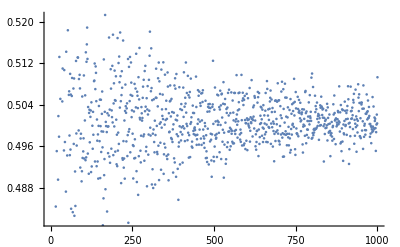

```mathematica
ListPlot[array]
```